Generando los puntos;
a = 1; b = 5;
datos = Table[{x,N[Sin[x]]},{x,a,b,1}]

{{1,0.841471},{2,0.909297},{3,0.14112},{4,-0.756802},{5,-0.958924}}

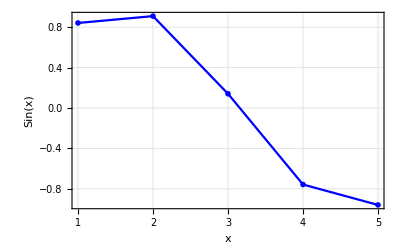

```mathematica
ListLinePlot[datos,
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["Sin(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue}
]
```

```mathematica
Utilizando la base de lagrange;
```

```mathematica
LagrangeBaseElements[xs_,i_]:=Table[If[i≠ j,(x-xs[[j+1]])/(xs[[i+1]]-xs[[j+1]]),1],{j,0,Length[xs]-1}];
LagrangeBase[xs_,i_]:=Apply[Times,LagrangeBaseElements[xs,i]];
```

```mathematica
LagrangeBase[datos[[All,1]],0]
```

1/24 (2-x) (3-x) (4-x) (5-x)

```mathematica
Total@Table[LagrangeBase[datos[[All,1]],i],{i,0,4}]
```

1/24 (2-x) (3-x) (4-x) (5-x)+1/6 (3-x) (4-x) (5-x) (-1+x)+1/4 (4-x) (5-x) (-2+x) (-1+x)+1/6 (5-x) (-3+x) (-2+x) (-1+x)+1/24 (-4+x) (-3+x) (-2+x) (-1+x)

```mathematica
Expand@Total@Table[LagrangeBase[datos[[All,1]],i],{i,0,4}]
```

1

```mathematica
LagrangeInterpolate[data_]:=Expand[data[[All,2]].Table[LagrangeBase[data[[All,1]],i],{i,0,Length[data]-1}]];
```

```mathematica
LagrangeInterpolate[datos]
```

-0.649331+2.36813 x-0.9503 x^2+0.0680069 x^3+0.00497029 x^4

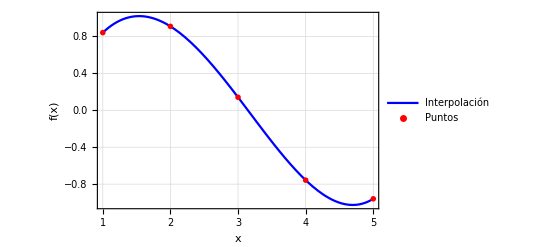

```mathematica
Show[
Plot[
{-0.6493310617421595+2.3681253386241785 x-0.9503004509420383 x^2+0.06800686584987492 x^3+0.004970293018039473 x^4},
{x,a,b},
PlotTheme->"Monochrome",FrameLabel->{Style["x",15], Style["f(x)",15]}, BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Blue},PlotLegends->{"Interpolación"}
],
ListPlot[datos,
PlotTheme->"Monochrome",BaseStyle->FontSize->13,PlotRangePadding->Automatic,GridLines->Automatic,Frame->True,PlotRange->All,PlotStyle->{Red},PlotLegends->{"Puntos"}
]
]
```

```mathematica
Comparando con la base polinomial, está mejor vista, sus curvas se ven muy buenas todo esto en comparación de la otra, además que en la gráfica de la interpolación polinomial, crecia desmesuradamente a partir de 5;
```